## lefty D_effective as a function of binding radius or k_d (constant k_off)

```mathematica
bindingrad = {2.87,3.90,4.92,6.19,8.92};
```

```mathematica
Subscript[k, on]= {0.1,0.25,0.5,1,2.83};
Subscript[d, eff]={20,11.11,8.11,6.21,3.57};
```

```mathematica
Subscript[k, off]=10000.;
```

```mathematica
Subscript[k, d]=Subscript[k, off]/Subscript[k, on]
```

{100000.,40000.,20000.,10000.,3533.57}

```mathematica
threadDataradius = Thread[{bindingrad,Subscript[d, eff]}]
```

{{2.87,20},{3.9,11.11},{4.92,8.11},{6.19,6.21},{8.92,3.57}}

```mathematica
threadData = Thread[{Subscript[k, on],Subscript[d, eff]}]
```

{{0.1,20},{0.25,11.11},{0.5,8.11},{1,6.21},{2.83,3.57}}

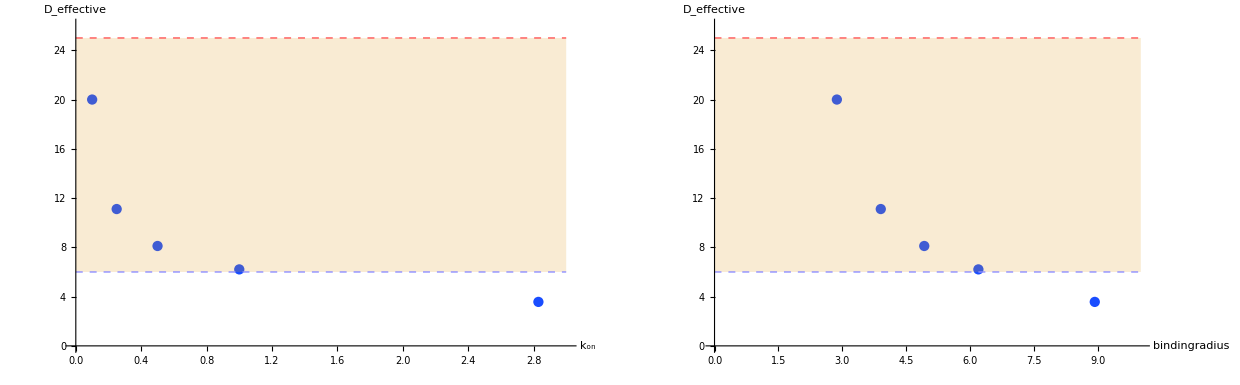

```mathematica
GraphicsGrid@{MapThread[Show[
ListPlot[#,PlotStyle->XYZColor[0,0,1,0.9],AxesLabel->{#2,"D_effective"},PlotRange->{{0,#3},{0,26}},ImageSize->Large],Plot[{6,25},{x,0,#3},PlotStyle->{{Dashed,Thick,Lighter[Lighter@Blue]},{Dashed,Thick,Lighter@Red}},Filling-> {2->{1}}]
]&,{{threadData,threadDataradius},{"k_on","bindingradius"},{3,10}}]}
```